## Parameters

```mathematica
Vcont[r_]:=ccont-αcont/r+σcont r;
V[r_,α_,σ_,c_]:=c-α/r+σ r;
Vsb[r_,α_,σ_,c_]:=HeavisideTheta[1.25/0.197-r](c-α/r+σ r)+HeavisideTheta[r-1.25/0.197](c-α/(1.25/0.197)+σ 1.25/0.197);
Veff[r_,l_,m_]:=(l(l+1))/(2m r^2);
ReV[r_,m_,α_,σ_,c_]:=-α m-α Exp[-m r]/r-Gamma[1/4]/(2^(3/4)√π)σ/((m^2 σ/α)^(1/4))ParabolicCylinderD[-1/2,√2(m^2 σ/α)^(1/4) r]+Gamma[1/4]/(2Gamma[3/4])σ/((m^2 σ/α)^(1/4))+c
μc=mc/2;
μb=mb/2;
(*from AR 1509.07366*)
σcont=0.415^2;
ccont=-0.176696;
αcont=0.50425;
mc=1.47164;
mb=4.882;
mbe=0.041;
(****)
```

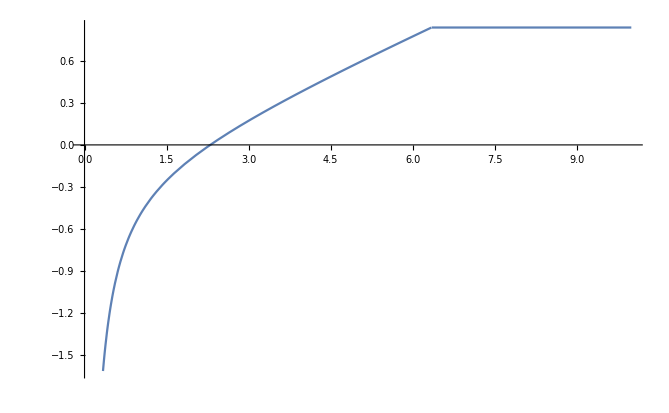

```mathematica
Plot[Vsb[r,αcont,σcont,ccont],{r,0,10}]
```

## Charmonium old

### Swave

```mathematica
{ccsvals,ccsvecs}=NDEigensystem[{-1/(2μc)Laplacian[u[x],{x}]+Vcont[x] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,30},4,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

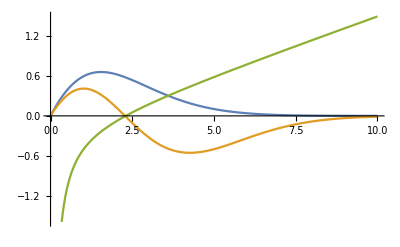

```mathematica
Plot[{ccsvecs[[1]][x],ccsvecs[[2]][x],Vcont[x]},{x,0,10}]
```

```mathematica
ccsvals
```

{0.152928,0.738566,1.16928,1.53686}

```mathematica
ccsmass=ConstantArray[2 mc,2]+Sort[ccsvals]
```

{3.09621,3.68185}

```mathematica
EMfactor=(ccsmass[[2]](ccsvecs[[1]][10^-100])/10^-100)^2/(ccsmass[[1]](ccsvecs[[2]][10^-100])/10^-100)^2
```

2.0689

```mathematica
{ccsvalsi,ccsvecsi}=NDEigensystem[{-1/(2μc)Laplacian[u[x],{x}]Exp[-2 ⅈ δ]+V[x Exp[ⅈ δ]] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,30},4,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

```mathematica
ccsvalsi
```

{0.152928+1.11666×10^-12 ⅈ,0.738566+1.70776×10^-12 ⅈ,1.16928+3.01912×10^-12 ⅈ,1.53686+8.25092×10^-13 ⅈ}

### Pwave

```mathematica
{ccpvals,ccpvecs}=NDEigensystem[{-1/(2μc)Laplacian[u[x],{x}]+V[x] u[x]+Veff[x,1,μc]u[x],DirichletCondition[u[x]==0,True]},u,{x,0,30},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

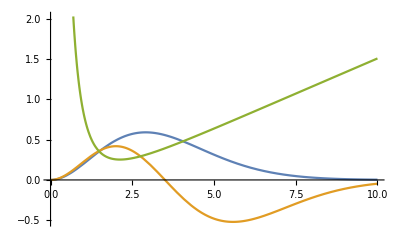

```mathematica
Plot[{ccpvecs[[1]][x],ccpvecs[[2]][x],V[x]+Veff[x,1,μc]},{x,0,10}]
```

```mathematica
ccpmass=ConstantArray[2 mc,2]+Sort[ccpvals][[;;2]]
```

{3.50904,3.96034}

## Bottomonium old

### Swave

```mathematica
{bbvals,bbvecs}=NDEigensystem[{-1/(2μb)Laplacian[u[x],{x}]+V[x] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,30},4,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

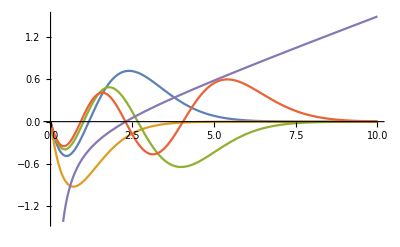

```mathematica
Plot[{bbvecs[[1]][x],bbvecs[[2]][x],bbvecs[[3]][x],bbvecs[[4]][x],V[x]},{x,0,10}]
```

```mathematica
bbmass=ConstantArray[2 mb,4]+Sort[bbvals][[;;4]]
```

{9.4599,10.019,10.3525,10.6217}

### Pwave

```mathematica
{bbpvals,bbpvecs}=NDEigensystem[{-1/(2μb)Laplacian[u[x],{x}]+V[x] u[x]+Veff[x,1,μb]u[x],DirichletCondition[u[x]==0,True]},u,{x,0,30},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

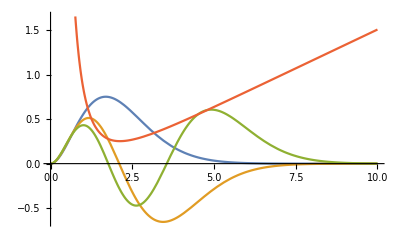

```mathematica
Plot[{bbpvecs[[1]][x],bbpvecs[[2]][x],bbpvecs[[3]][x],V[x]+Veff[x,1,μc]},{x,0,10}]
```

```mathematica
cbbpmass=ConstantArray[2 mb,3]+Sort[bbpvals]
```

{9.92524,10.2681,10.5432}

## New parameters

### Bottomonium Fit

```mathematica
Off[NDEigenvalues::femcnsd]
```

```mathematica
bbswavePDG={10.02326,9.4603,10.3552,10.5794};
bbswavePDGe={0.00031,0.00026,0.0002,0.0012};
bbswavePDG3={10.02326,9.4603,10.3552};
bbswavePDG3e={{10.02326,0.00031},{9.4603,0.00026},{10.3552,0.0002}};
bbpwavePDG={9.88814,10.252,10.534};
```

```mathematica
mbrand:=RandomVariate[NormalDistribution[mb,mbe]];
bbswavePDG3rand:={RandomVariate[NormalDistribution[bbswavePDG3e[[1,1]],bbswavePDG3e[[1,2]]]],RandomVariate[NormalDistribution[bbswavePDG3e[[2,1]],bbswavePDG3e[[2,2]]]],RandomVariate[NormalDistribution[bbswavePDG3e[[3,1]],bbswavePDG3e[[3,2]]]]};
```

```mathematica
bbswavemass3rand[α_,σ_,c_]:=2mb+NDEigenvalues[{-1/mbrand Laplacian[u[x],{x}]+Vsb[x,α,σ,c] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,20},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

```mathematica
res={{},{},{}};
SetSharedVariable[res];
Module[{al,sig,const},
ParallelDo[{al,sig,const}={α,σ,c}/.Quiet[FindRoot[bbswavePDG3rand==bbswavemass3rand[α,σ,c],{{α,αcont},{σ,σcont},{c,ccont}}]];
res[[1]]=Append[res[[1]],al];
res[[2]]=Append[res[[2]],sig];
res[[3]]=Append[res[[3]],const];,{i,1,2}]]//AbsoluteTiming
```

{33.4194,Null}

```mathematica
αfinal1={Mean[res[[1]]],StandardDeviation[res[[1]]]}
σfinal1={Mean[res[[2]]],StandardDeviation[res[[2]]]}
cfinal1={Mean[res[[3]]],StandardDeviation[res[[3]]]}
```

{0.514204,0.00239628}

{0.169415,0.00098697}

{-0.158056,0.00170593}

```mathematica
αfinal={0.5137193759431391,0.0024666827878353577}; (*2k run*)
σfinal={0.16955497884544793,0.0008581023195660334};
cfinal={-0.15956635071361625,0.0024752900407607015};
```

```mathematica
bbswavemass[α_,σ_,c_]:=2mb + NDEigenvalues[{-1/(2μb)Laplacian[u[x],{x}]+Vsb[x,α,σ,c] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,20},4,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
bbpwavemass[α_,σ_,c_]:=2mb+NDEigenvalues[{-1/(2μb)Laplacian[u[x],{x}]+Vsb[x,α,σ,c] u[x]+Veff[x,1,μb]u[x],DirichletCondition[u[x]==0,True]},u,{x,0,20},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

```mathematica
bbswavemass[αfinal[[1]],σfinal[[1]],cfinal[[1]]]
```

{10.0233,9.46028,10.3552,10.5949}

```mathematica
bbpwavemass[αfinal[[1]],σfinal[[1]],cfinal[[1]]]
```

{9.93142,10.2727,10.5393}

```mathematica
bbswavePDG
```

{10.0233,9.4603,10.3552,10.5794}

```mathematica
bbpwavePDG
```

{9.88814,10.252,10.534}

```mathematica
bbswavePDG-bbswavemass[αfinal[[1]],σfinal[[1]],cfinal[[1]]]
```

{1.4877×10^-6,0.0000193632,0.000014367,-0.0155216}

```mathematica
bbpwavePDG-bbpwavemass[αfinal[[1]],σfinal[[1]],cfinal[[1]]]
```

{-0.0432819,-0.0206885,-0.00530149}

```mathematica
(*diff[α_?NumericQ,σ_?NumericQ,c_?NumericQ]:=Norm[Join[bbswavePDG-bbswavemass[α,σ,c],bbpwavePDG-bbpwavemass[α,σ,c]]]
diffs13[α_?NumericQ,σ_?NumericQ,c_?NumericQ]:=Norm[bbswavePDG3-bbswavemass3[α,σ,c]];
diffsall[α_?NumericQ,σ_?NumericQ,c_?NumericQ]:=Norm[bbswavePDG-bbswavemass[α,σ,c]];
diffpall[α_?NumericQ,σ_?NumericQ,c_?NumericQ]:=Norm[bbpwavePDG-bbpwavemass[α,σ,c]];
diffcheck[α_?NumericQ,σ_?NumericQ,c_?NumericQ]:=Norm[Join[bbswavemass[αcont,σcont,ccont]-bbswavemass[α,σ,c],bbpwavemass[αcont,σcont,ccont]-bbpwavemass[α,σ,c]]]*)
```

```mathematica
(*FindMinimum[diff[α,σ,c],{{α,0.5,0.,1.},{σ,0.415^2,0.,1.0},{c,-0.17,-1.,0.}},Method->"PrincipalAxis"]*)
```

```mathematica
(*FindMinimum[diffcheck[α,σ,c],{{α,0.5,0.,1.},{σ,0.415^2,0.,1.0},{c,-0.17,-1.,0.}},Method->"PrincipalAxis"]*)
```

```mathematica
(*NMinimize[{diff[α,σ,c],0≤α≤1,0≤σ≤1,-1≤c≤0},{α,σ,c}]//AbsoluteTiming*)
```

### Charmonium Fit

```mathematica
ccswavePDG={{3.0969,0.000006},{3.686097,0.0000025}};
ccswavePDG1={3.0969};
```

```mathematica
ccswavemass1[m_]:=2m+NDEigenvalues[{-1/m Laplacian[u[x],{x}]+Vsb[x,αfinal[[1]],σfinal[[1]],cfinal[[1]]] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,20},1,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

```mathematica
FindRoot[ccswavemass1[m]==ccswavePDG1,{m,mc}]
```

NDEigenvalues::femcnmd: The PDE coefficient {{1/m}} does not evaluate to a numeric matrix of dimensions {1,1} at the coordinate {10.}.

General::stop: Further output of NDEigenvalues::femcnmd will be suppressed during this calculation.

{m→1.46906}

```mathematica
mcfinal=1.4690612135716832;
```

```mathematica
mcold=1.4689783072176936;
```

```mathematica
ccswavemass[m_]:=2m+NDEigenvalues[{-1/m Laplacian[u[x],{x}]+Vsb[x,αfinal[[1]],σfinal[[1]],cfinal[[1]]] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,20},2,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
ccpwavemass[m_]:=2m+NDEigenvalues[{-1/m Laplacian[u[x],{x}]+Vsb[x,αfinal[[1]],σfinal[[1]],cfinal[[1]]] u[x]+Veff[x,1,m/2]u[x],DirichletCondition[u[x]==0,True]},u,{x,0,20},2,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

```mathematica
ccswavemass[mcfinal]
```

{3.0969,3.66801}

```mathematica
ccpwavemass[mcfinal]
```

{3.50822,3.80811}

```mathematica
ccfinal=NDEigensystem[{-1/mcold Laplacian[u[x],{x}]+Vsb[x,αfinal[[1]],σfinal[[1]],cfinal[[1]]] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,20},2,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

```mathematica
2mcold +ccfinal[[1]]
```

{3.09675,3.66786}

```mathematica
EMfactor=((2mcold +ccfinal[[1,2]]) (ccfinal[[2,1]][10^-100])/10^-100)^2/((2mcold +ccfinal[[1,1]])(ccfinal[[2,2]][10^-100])/10^-100)^2
```

2.35631